```mathematica
ClearAll["Global`*"]
```

## Import

```mathematica
(*parampath="/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-ba130/fit_params.dat";
params=Flatten[Import[parampath]];*)
I1=27;
I2=22;
I3=43;
```

## Calculate the terms t1 and t2 (normalized to the spin value I)

The components t_1and t_2 are given without the spin dependence since the coefficients w_(1,2) will cancel out their spins in the fraction part

```mathematica
t1=1/(2*I2)+1/(2*I1)-2 1/(2*I3);
t2=1/(2*I2)-1/(2*I1);
w1=Sqrt[1/2(t1/Sqrt[t1^2-t2^2]+1)];
w2=Sqrt[1/2(t1/Sqrt[t1^2-t2^2]-1)];
```

#### The deformation parameters (Chen et al.) CDFT calculations

```mathematica
beta=0.24;
gamma=21.5;
A=130;
Z=56;
R=1.2*A^(1/3);
```

### Intrinsic quadrupole moment Q_0

```mathematica
Q0[beta_]:=3/(√(5π))R^2*Z*beta(1+0.16beta);
Q20[beta_,gamma_]:=Q0[beta]*Cos[gamma*π/180];
Q22[beta_,gamma_]:=Q0[beta]/(√2)Sin[gamma*π/180];
```

### Numerical values

```mathematica
Grid[{{"Parameters","Calculated values","Observations"},{"β_2",beta,"Taken from Ref."},{"γ",gamma"","Taken from Ref."},{"w_1",N[w1],"from 𝒫_fit"},{"w_2",N[w2],"from 𝒫_fit"},{"Q_0",Q0[beta],"-"},{"Q_20",Q20[beta,gamma],"-"},{"Q_22",Q22[beta,gamma],"-"}},Frame->All]
```

Parameters | Calculated values | Observations
β_2 | 0.24 | Taken from Ref.
γ | 21.5  | Taken from Ref.
w_1 | 1.00711 | from 𝒫_fit
w_2 | 0.119464 | from 𝒫_fit
Q_0 | 390.376 | -
Q_20 | 363.213 | -
Q_22 | 101.168 | -

## Intraband transition probabilities

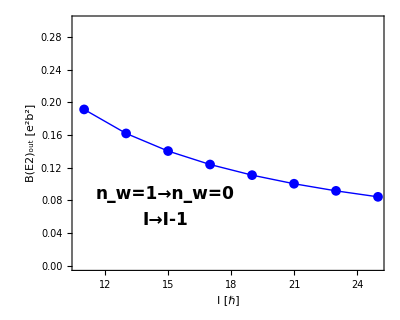

ff= 0.509047

0.376045

0.318192

0.275766

0.243323

0.21771

0.196976

0.179847

0.16546

```mathematica
quench1=10^-4/2;
quench2=quench1*10;
BE2in[beta_,gamma_]:=5/(16π)*Q22[beta,gamma]^2*quench2;
BE2outPlus[n_,I_,beta_,gamma_]:=5/(16π)*(n+1)/I*(√3 Q20[beta,gamma]*w2+√2 Q22[beta,gamma]*w1)^2;
BE2outMinus[n_,I_,beta_,gamma_]:=5/(16π)*n/I*(√3 Q20[beta,gamma]*w1+√2 Q22[beta,gamma]*w2)^2*quench1;
be2Plot=ListPlot[Table[{x,BE2outMinus[1,x,beta,gamma]},{x,11,25,2}],Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,PlotRange->{All,{0,0.3}},AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameLabel->{"I [ℏ]","B(E2)_out [e^2b^2]"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},FrameStyle->Directive[Black,Thick],Epilog->{Inset[Style["n_w=1→n_w=0",Bold,17,Black],Scaled[{0.3,0.3}]],Inset[Style["I→I-1",Bold,Italic,17,Black],Scaled[{0.3,0.2}]]}];
be2Plot
Export["/Users/basavyr/Documents/Work/PhD/Annual-Session-2022/Presentation/Figs/ba130-EM.pdf",be2Plot,ImageResolution->1200];
ff=BE2in[beta,gamma];
Print["ff= ",ff]
BE2outMinus[1,11,beta,gamma]/ff
BE2outMinus[1,13,beta,gamma]/ff
BE2outMinus[1,15,beta,gamma]/ff
BE2outMinus[1,17,beta,gamma]/ff
BE2outMinus[1,19,beta,gamma]/ff
BE2outMinus[1,21,beta,gamma]/ff
BE2outMinus[1,23,beta,gamma]/ff
BE2outMinus[1,25,beta,gamma]/ff
```